# Field Effect

## Looking at effect of Field on spatial current distribution

#### Initialize Constants and Stuff

```mathematica
Φ0=1;
Iinitial=1; (*Just make all the constants 1 for now. Definiely fix this in later versions to control for physical constants, but now just interested in phenomena*)
Ifunc[Φ_]:=Iinitial Abs[Sin[π Φ/Φ0]/(π Φ/Φ0)]
```

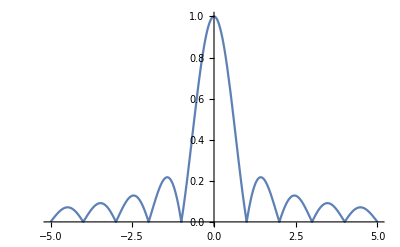

```mathematica
Plot[Ifunc[Φ],{Φ,-5Φ0,5Φ0},PlotRange->{0,1}]
```